## Осипов Н.С., ПМ - 1801 1.1.11. Дробно-рациональное интерполирование а) Метод неопределенных коэффициентов

```mathematica
ratIn[l_,r_,f_]:=Module[{p,q,n,xlst,lst={},
res,Pa,Pb},
If[l<r, n= r-l;xlst = Range[l,r,1.],
If[r<l,n=l-r;xlst = Range[r,l,1.],
Return[Text[Style["Error",14]]]]];
If[EvenQ[n]==True,
q=p=n/2,q=(n-1)/2;p=n-q];
Clear[a,b,x];
Pa=Normal@Plus@@(Subscript[a, #] x^#&/@Range[0,p]⟦;;-2⟧);(*Subscript[a, 0]+Subscript[a, 1] x+Subscript[a, 2] x^2+..+Subscript[a, p] x^p*)
Pa += x^p;
Pb=Normal@Plus@@(Subscript[b, #] x^#&/@Range[0,q]);(*Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2+..+Subscript[b, q] x^q*)
For[i=1,i≤n+1,i++,
AppendTo[lst,((Pa-Pb*N@(f/.x:>xlst⟦i⟧))==0)/.x:>xlst⟦i⟧]];(*СЛАУ*)
res=Flatten@Solve[And@@lst];(*решение СЛАУ*)
(Pa=Pa/.#)&/@res;
(Pb=Pb/.#)&/@res;
Pa/Pb]
```

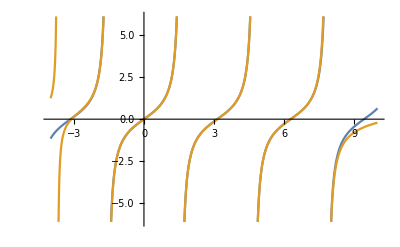
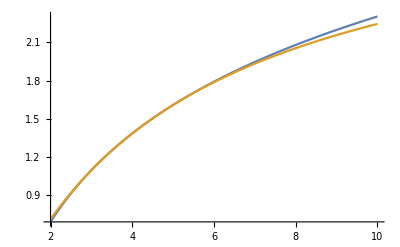
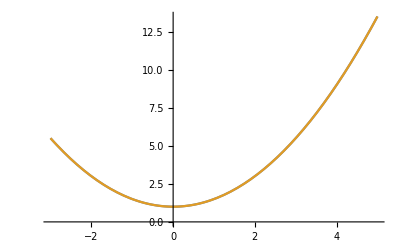
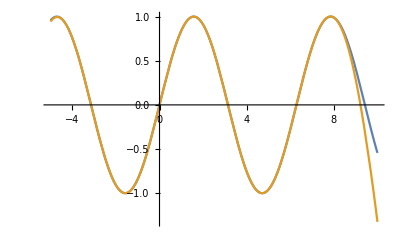
f(x) | Pa/Pb | Plot
Tan[x], x ϵ [-4,10]

Pa/Pb,     x ϵ [-3,8] | (0.-3526.33 x+225.291 x^2+475.13 x^3-33.8052 x^4-11.5813 x^5+x^6)/(-3548.36+239.34 x+1675.18 x^2-126.292 x^3-93.4144 x^4+10.5464 x^5) | -Graphics-
Log[x], x ϵ [2,10]

Pa/Pb,     x ϵ [3,5] | (-0.749469+x)/(1.1598+0.296241 x) | -Graphics-
1+x^2/2, x ϵ [-3,5]

Pa/Pb,     x ϵ [-1,2] | (2.+x^2)/(2.+1.35694×10^-16 x) | -Graphics-
Sin[x], x ϵ [-5,10]

Pa/Pb,     x ϵ [-4,8] | (0.-3457.33 x+353.343 x^2+443.642 x^3-45.6685 x^4-9.45839 x^5+x^6)/(-3457.77+353.484 x-132.01 x^2+13.0338 x^3-2.88359 x^4+0.310036 x^5-0.03367 x^6) | -Graphics-

```mathematica
f1=Tan[x];
res1=ratIn[-3,8,f1];
plot1=Plot[{f1,res1},{x,-4,10}];
f2=Log[x];
res2=ratIn[3,5,f2];
plot2=Plot[{f2,res2},{x,2,10}];
f3=1+x^2/2;
res3=ratIn[-1,2,f3];
plot3=Plot[{f3,res3},{x,-3,5}];
f4=Sin[x];
res4=ratIn[-4,8,f4];
plot4=Plot[{f4,res4},{x,-5,10}];
Grid[{{Text[Style["f(x)",14]],Text[Style["Pa/Pb",14]],Text[Style["Plot",14]]},
{Text[Style[ToString@f1<>", x ϵ [-4,10]\n\nPa/Pb,     x ϵ [-3,8]",14]],Text[Style[res1,14]],plot1},
{Text[Style[ToString@f2<>", x ϵ [2,10]\n\nPa/Pb,     x ϵ [3,5]",14]],Text[Style[res2,14]],plot2},
{Text[Style["1+x^2/2"<>", x ϵ [-3,5]\n\nPa/Pb,     x ϵ [-1,2]",14]],Text[Style[res3,14]],plot3},
{Text[Style[ToString@f4<>", x ϵ [-5,10]\n\nPa/Pb,     x ϵ [-4,8]",14]],Text[Style[res4,14]],plot4}
},
Frame->All]
```